```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/shivasankark.a/Documents/Research_work/Tools/PICSHEP/Models/AGN_U1X

```mathematica
tBH=10^9*365*24*3600;
RS = 4.84814*10^-6*0.1986 (*pc*);
rs = 13*10^3(*pc*);
ρs = 0.35 (*GeV/cm^3*);
Rsp=0.7*10^3(*pc*);........
rh=0.65(*pc*);
ri=4*RS;
```

((Null...)...)..

```mathematica
RS*30
```

0.0000288852

```mathematica
f[α_,r_]:=r^-α(r^3/(3-α)+12*RS*r^2/(α-2)-48*RS^2 r/(α-1)+64*RS^3/α);

Num[α_]:=10^7/(4π(f[α,rh]-f[α,ri]))*(1.988*10^30*5.62*10^26);
ρN[α_]:=Which[α==3/2,Num[α]/rh^(3/2)*1/((3.086*10^18)^3),α==7/3,Num[α]/Rsp^(7/3)*1/((3.086*10^18)^3)];

ρNp[α_]:=(*ρN[α]*(rs/Rsp)^(7/3)*)Num[α]*rh^(5/6)/Rsp^(7/3)*1/((3.086*10^18)^3);

ρc[mχ_,σ_]:=mχ/(σ*10^-26*tBH)(*GeV/cm^3*); 

ρα[α_,r_]:=Which[α==3/2,
			Which[ri<=r<=rh,ρN[3/2]*(1-4*RS/r)^3(rh/r)^(3/2),r>=rh,ρNp[3/2]*(Rsp/r)^(7/3)],
α==7/3,
			If[r>=ri,ρN[7/3]*(1-4 RS/r)^3(Rsp/r)^(7/3),0]];
ρNFW[r_]:=ρs*(r/rs)^-1(1+r/rs)^-2;
```

```mathematica
ρχ[α_,r_,mχ_,σ_]:=Which[r<=ri,0,ri<=r<=Rsp,ρα[α,r]*ρc[mχ,σ]/(ρc[mχ,σ]+ρα[α,r]),r>=Rsp,ρNFW[r]*ρc[mχ,σ]/(ρc[mχ,σ]+ρNFW[r])]
```

```mathematica
ρχ[7/3,10^-5,10^-3,10^-8]
```

3.17063×10^14

```mathematica
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
rval = N@logspace[2000,10^-9,10^4];
```

```mathematica
dat1={};
m=10^-0(*GeV*);
Do[
AppendTo[dat1,{rval[[i]],ρχ[7/3,rval[[i]],m,10^-8],ρχ[7/3,rval[[i]],m,3],ρχ[3/2,rval[[i]],m,10^-8],ρχ[3/2,rval[[i]],m,3]}],{i,Length[rval]}
]
(*Export["DM_density_mchi=1keV.txt",dat1,"Table"]; *)
```

```mathematica
dat1={};
m=10^0(*GeV*);
Do[
AppendTo[dat1,{rval[[i]],ρχ[7/3,rval[[i]],m,10^-10],ρχ[7/3,rval[[i]],m,0.01],ρχ[7/3,rval[[i]],m,3],ρχ[3/2,rval[[i]],m,10^-10],ρχ[3/2,rval[[i]],m,0.01],ρχ[3/2,rval[[i]],m,3]}],{i,Length[rval]}
]
```

```mathematica
dat1
```

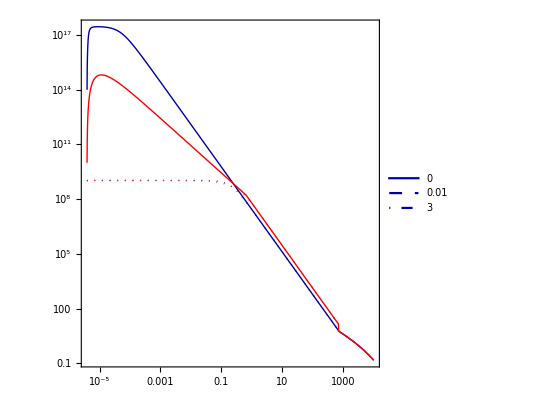

```mathematica
ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]](*,dat1[[All,{1,6}]],dat1[[All,{1,7}]]*)},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->(*{{10^-6,10^4},{10^1,10^20}}*)All,PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dotted],(*Directive[Darker[Blue],Thick,Dashed],*)Directive[Red,Thick],Directive[Red,Thick,Dotted],Directive[Red,Thick,Dashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18],  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Darker[Blue],Thick,DotDashed],Directive[Red,Thick],Directive[Red,Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Red,,Thick,DotDashed]},{Style["0",25,Black],Style["0.01",25,Black],Style["3",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.8},{1,1}}]]
```

```mathematica
rmin=RS*30;
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
rval = N@logspace[2000,rmin,10^4];
dat1={};
m=10^-6(*GeV*);
AbsoluteTiming[Do[
AppendTo[dat1,{rval[[i]],NIntegrate[ρχ[7/3,r,m,10^-8],{r,rmin,rval[[i]]}],NIntegrate[ρχ[7/3,r,m,3],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,10^-8],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,3],{r,rmin,rval[[i]]}]}],{i,Length[rval]}
]]
dat1[[All,{2,3,4,5}]] = dat1[[All,{2,3,4,5}]]*3.086*10^18;
Export["DM_Sigma_mchi=1keV.txt",dat1,"Table"];
```

{136.3,Null}

```mathematica
NIntegrate[ρχ[7/3,r,10^3,10^-8],{r,RS*30,10^4}]
```

1.80339×10^13

```mathematica
rmin=RS*30;
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
rval = N@logspace[500,rmin,10^4];
dat1={};
m=10^0(*GeV*);
AbsoluteTiming[Do[
AppendTo[dat1,{rval[[i]],NIntegrate[ρχ[7/3,r,m,10^-10],{r,rmin,rval[[i]]}],NIntegrate[ρχ[7/3,r,m,0.01],{r,rmin,rval[[i]]}],NIntegrate[ρχ[7/3,r,m,3],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,10^-10],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,0.01],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,3],{r,rmin,rval[[i]]}]}],{i,Length[rval]}
]]
```

{49.8665,Null}

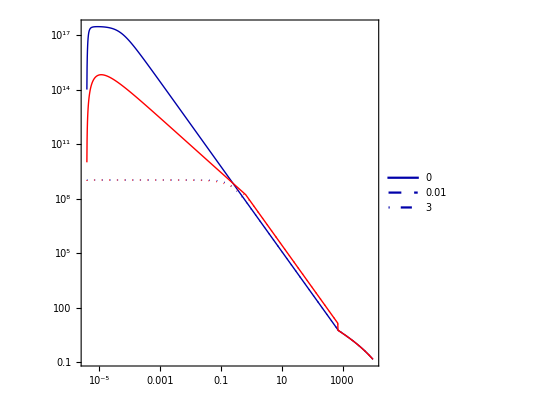

```mathematica
ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]](*,dat1[[All,{1,6}]],dat1[[All,{1,7}]]*)},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->(*{{10^-6,10^4},{10^20,10^34}}*)All,PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dotted],(*Directive[Darker[Blue],Thick,Dashed],*)Directive[Red,Thick],Directive[Red,Thick,Dotted],Directive[Red,Thick,Dashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18],  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Darker[Blue],Thick,DotDashed],Directive[Red,Thick],Directive[Red,Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Red,,Thick,DotDashed]},{Style["0",25,Black],Style["0.01",25,Black],Style["3",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.8},{1,1}}]]
```

```mathematica
(*Σ/mχ vs mχ*)
rmin=RS*4;
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
m =  N@logspace[100,10^-6,10^3];
rval = 5*10^3;
dat1={};
AbsoluteTiming[Do[
AppendTo[dat1,{m[[i]],NIntegrate[ρχ[7/3,r,m[[i]],10^-8],{r,rmin,rval}],NIntegrate[ρχ[7/3,r,m[[i]],3],{r,rmin,rval}],NIntegrate[ρχ[3/2,r,m[[i]],10^-8],{r,rmin,rval}],NIntegrate[ρχ[3/2,r,m[[i]],3],{r,rmin,rval}]}],{i,Length[m]}
]]
dat1[[All,{2,3,4,5}]] = dat1[[All,{2,3,4,5}]]*3.086*10^18/m;
Export["Sigmamchi_vs_mchi.txt",dat1,"Table"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.00273689}. NIntegrate obtained 2.83683×10^11 and 2.08648×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.00269835}. NIntegrate obtained 3.38794×10^12 and 6.37449×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {5.1844233538755531605368449127313468238753557670861482620239257813×10^-6}. NIntegrate obtained 3.80504×10^12 and 1.87978×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{11.6358,Null}

Sigmamchi_vs_mchi.txt

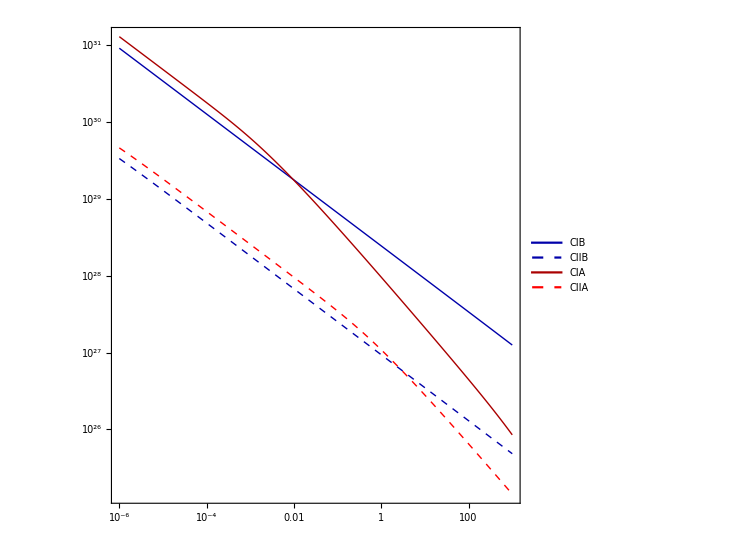

```mathematica
ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]]},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->(*{{10^-6,10^4},{10^20,10^34}}*)All,PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashed],Directive[Darker[Red],Thick],Directive[Red,Thick,Dashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18],  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashed],Directive[Darker[Red],Thick],Directive[Red,Thick,Dashed]},{Style["CIB",25,Black],Style["CIIB",25,Black],Style["CIA",25,Black],Style["CIIA",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.95},{1,1}}]]
```